```mathematica
DateString[]
```

Sun 10 Apr 2016 15:55:15

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/harold/Organised/Active papers/Euler/Distribution

## Draw diagrams

```mathematica
multiString[s_]:=StringJoin@@Table[s,{i,100}]
```

```mathematica
multiString["x"]
```

xxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxx

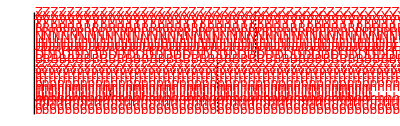

```mathematica
height=.28;
gap=0.1;
singleLineWidth[s_]:=1/50*Total@Map[Switch[#,
Alternatives@@Characters@"OQC",1.75,
Alternatives@@Characters@"UG",1.85,
Alternatives@@Characters@"w",1.75,
Alternatives@@Characters@"m",2,
Alternatives@@Characters@"ijl",.55,
Alternatives@@Characters@"ABDEFGHJKLNPRSTVXYZ",1.6,
Alternatives@@Characters@"I",0.8,
Alternatives@@Characters@"yskc",1.18,
"W",2.25,
"M",2.005,
_,1.325
]&,Characters[s]];
Graphics[{
chars=Characters["abcdefghijklmnopqrstuvwxyzABCDEFGHIJKLMNOPQRSTUVWXYZ"];
Black,Line[{{0,0},{0,1}}],
Table[
{y=c/52;
dw=singleLineWidth[multiString@chars[[c]]];
Black,Line[{{dw,y-.5/52},{dw,y+.5/52}}],
Red,Text[Style[multiString@chars[[c]],12],{0,y},{-1,0}]
},
{c,2,52,2}
]
},ImageSize->{Automatic,300}]
```

```mathematica
WeightedStringLength[s_]:=Max[singleLineWidth/@StringSplit[s,"\n"]];
forcewidth=0;
maxwidth=0;
box[{xc_,yc_},name_,colour_:White]:=
Module[{ww,h},
h=height;
ww=WeightedStringLength[name];
maxwidth=Max[maxwidth,ww];
If[forcewidth≠0,ww=maxwidth];
xmin=xc-ww;xmax=xc+ww;ymin=yc-h/2;ymax=yc+h/2;
{If[!NumericQ[colour],Lighter@Lighter@colour,FaceForm[None]],
EdgeForm[Directive[Black]],
If[!NumericQ[colour],{},{
FaceForm@Lighter@Lighter@Gray,EdgeForm[None],
If[colour<.5,
{Rectangle[{xmin,ymin},{xmin+.2*(xmax-xmin),ymax}],
Rectangle[{xmin+.3*(xmax-xmin),ymin},{xmin+.45*(xmax-xmin),ymax}],
Rectangle[{xmin+.55*(xmax-xmin),ymin},{xmin+.7*(xmax-xmin),ymax}],
Rectangle[{xmin+.8*(xmax-xmin),ymin},{xmax,ymax}]},
Rectangle[{.95*(xmax-xmin)+xmin,ymin},{xmax,ymax}]
]
}],
Rectangle[{xmin,ymin},{xmax,ymax},RoundingRadius->.015],
Black,Text[Style[name,12],{xc,yc}]}
];
highlight[c_,partial_:0]:=Module[{s},
{EdgeForm[{Thick,c}],FaceForm[None],
Rectangle[{xmin,ymin},{xmax,ymax},RoundingRadius->.015],
If[partial≠0,{Thickness[.01],White,
Line[{{s=.95*(xmax-xmin)+xmin,ymin},{xmax,ymin},{xmax,ymax},{s,ymax}}]
},{}]
}
];
```

```mathematica
caption[s_]:=Text[Style[s,17,Bold],{0,1.5height}];
description[s_,pos_]:=Text[Style[s,14],pos];
```

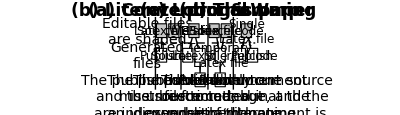

```mathematica
forcewidth=0;
Clear[c]
c[]:=Module[{t},
t=Graphics[{Arrowheads[Medium],
caption["(b) Literate programming"],
Arrow[{{0,0},{.25,-.5+height/2}}],
Arrow[{{0,0},{-.25,-.5+height/2}}],
box[{0,0},"WEB file",Gray],
box[{-.25-gap,-.5},"Source code"],
Arrow[{{.25+gap,-.5},{.25+gap,-1+height/2}}],
box[{.25+gap,-.5},"Latex file"],
box[{.25+gap,-1},"Publish"],
description["The published document\nmust be formatted in\nan idiosyncratic “literate\nprogramming” style.",{0,-1.5}],
Translate[{caption["(c) Loom & Warp"],
Arrow[{{-.250,0},{-0.1,-.5+height/2}}],
Arrow[{{.25,0},{0.1,-.5+height/2}}],
box[{-.250-gap,0},"Latex file",Gray],
box[{.25+gap,-0},"Source code",Gray],
Arrow[{{0,-.5},{0,-1+height/2}}],
box[{0,-.5},"Temporary\nLatex file"],
box[{0,-1},"Publish"],
description["The published document\nis unrestricted, but at the\nexpense of managing\nseveral source files.",{0,-1.5}]
},{1.5,0}],
Translate[{caption["(a) Conventional"],
Arrow[{{-.25-gap,0},{-0.25-gap,-.5+height/2}}],
box[{-.250-gap,0},"Latex file",Gray],
box[{.25+gap,-0},"Source code",Gray],
box[{-0.25-gap,-.5},"Publish"],
description["The published document\nand the source code\nare independent and\nprobably inconsistent.",{0,-1.5}]},{-1.5,0}],
Translate[{
caption["(d) This paper"],
Arrow[{{0,0},{.25,-.5+height/2}}],
Arrow[{{0,0},{-.25,-.5+height/2}}],
box[{0,0},"Single\nLatex file",Gray],
box[{-.25-gap,-.5},"Source code"],
box[{.25+gap,-.5},"Publish"],
description["There is only one source\nfile to manage, and the\npublished document is\nunrestricted.",{0,-1.5}]},{3,0}],

Thick,Table[Line[{{i,+height},{i,-1.2}}],{i,{-2.2,-.74,.8,2.25}}],
Thickness[Medium],Dashed,
Line[{{-2.95,-.25},{3.5,-.25}}],
Text[Style["Editable files\nare shaded",14],{-2.65,-0},{0,0}],
Text[Style["Generated\nfiles",14],{-2.65,-.5},{0,0}]
},ImageSize->{Automatic,300}
];
forcewidth=maxwidth;
Return[t]
];
c[] (* find out box sizes *);c[]
```

Various sorts of writing about programs. Approach (a) is very common: a paper is written about a program, but there is no automatic relation between the paper and the 
program, and there are likely errors in the paper. In (b) a single WEB file is the source of both the program source code and any documentation; in this case, the code and paper are side-by-side when they are edited. In (c)

```mathematica
(*Export["figures/diagram.pdf",c[]]*)
```

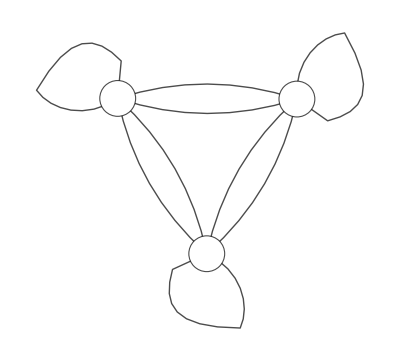

```mathematica
cg=Graph[Flatten@Table[u->v,{u,3},{v,3}],VertexSize->Medium,EdgeStyle->Black,VertexStyle->White,VertexLabels->Table[u->Placed[Style[Switch[u,1,"C",2,"B",3,"A"],Italic,FontFamily->"Times",Bold,20],
Center
],{u,3}],EdgeShapeFunction->GraphElementData[{"Arrow","ArrowSize"->.05}]]
```

```mathematica
Export["figures/K3.pdf",cg]
```

figures/K3.pdf

```mathematica
divider[dy_]:={
Thickness[Medium],Dashed,
Line[{{-2.95,-.25+dy},{1.1,-.25+dy}}],
Text[Style["Editable files\nare shaded",14],{-2.65,dy-0},{0,0}],
Text[Style["Generated\nfiles",14],{-2.65,dy-.5},{0,0}]}
```

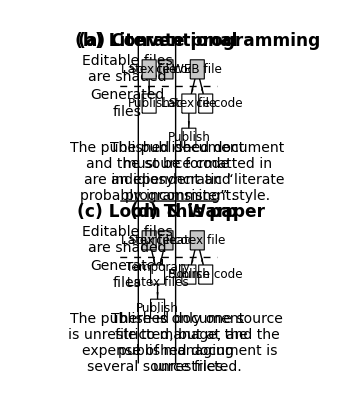

```mathematica
forcewidth=0;
Clear[c]
c[]:=Module[{t},
t=Graphics[{Arrowheads[Medium],
Translate[{caption["(a) Conventional"],
Arrow[{{-.25-gap,0},{-0.25-gap,-.5+height/2}}],
box[{-.250-gap,0},"Latex file",Gray],
box[{.25+gap,-0},"Source code",Gray],
box[{-0.25-gap,-.5},"Publish"],
description["The published document\nand the source code\nare independent and\nprobably inconsistent.",{0,-1.5}]},{-1.4,0}],
Translate[{caption["(b) Literate programming"],
Arrow[{{0,0},{.25,-.5+height/2}}],
Arrow[{{0,0},{-.25,-.5+height/2}}],
box[{0,0},"WEB file",Gray],
Arrow[{{-.25-gap,-.5},{-.25-gap,-1+height/2}}],
box[{-.25-gap,-.5},"Latex file"],
box[{.25+gap,-.5},"Source code"],
box[{-.25-gap,-1},"Publish"],
description["The published document\nmust be formatted in\nan idiosyncratic “literate\nprogramming” style.",{0,-1.5}]},{.25,0}],
Translate[{caption["(c) Loom & Warp"],
Arrow[{{-.250,-height/2},{-0.1,-.5+height/2}}],
Arrow[{{.25,-height/2},{0.1,-.5+height/2}}],
box[{-.250-gap,0},"Latex file",Gray],
box[{.25+gap,-0},"Source code",Gray],
Arrow[{{0,-.5},{0,-1+height/2}}],
box[{0,-.5},"Temporary\nLatex files"],
box[{0,-1},"Publish"],
description["The published document\nis unrestricted, but at the\nexpense of managing\nseveral source files.",{0,-1.5}]
},{-1.4,-2.5}],
Translate[{
caption["(d) This paper"],
Arrow[{{0,0},{.25,-.5+height/2}}],
Arrow[{{0,0},{-.25,-.5+height/2}}],
box[{0,0},"Latex file",Gray],
box[{-.25-gap,-.5},"Publish"],
box[{.25+gap,-.5},"Source code"],
description["There is only one source\nfile to manage, and the\npublished document is\nunrestricted.",{0,-1.5}]},{.25,-2.5}],
Thin,
Table[Line[{{i,.2+height},{i,-4.3}}],{i,{-2.2,-.65(*,.8,2.25*)}}],
Line[{{-2.95,-.25+-1.675},{1.1,-.25+-1.675}}],
divider[0],divider[-2.5],
},ImageSize->{Automatic,600}
];
forcewidth=maxwidth;
Return[t]
];
c[] (* find out box sizes *);c[]
```

```mathematica
Export["figures/literateProgramming.pdf",c[]]
```

figures/literateProgramming.pdf

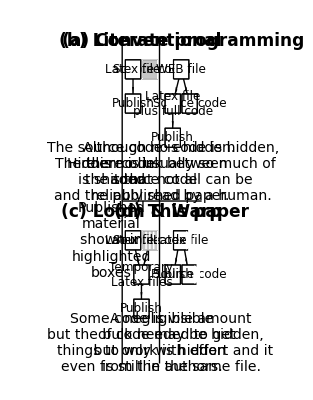

```mathematica
dividertwo[dy_]:={
Text[Style["Hidden code\nis shaded",14],{-2.65,dy-0},{0,0}],
Text[Style["Published\nmaterial\nshown in\nhighlighted\nboxes",14],{-2.65,dy-1},{0,0}]};
forcewidth=0;
Clear[c]
c[]:=Module[{t},
t=Graphics[{Arrowheads[Medium],
Translate[{caption["(a) Conventional"],
Arrow[{{-.25-gap,0},{-0.25-gap,-.5+height/2}}],
box[{-.250-gap,0},"Latex file"],highlight[Black],
box[{.25+gap,-0},"Source code",Gray],highlight[White],
box[{-0.25-gap,-.5},"Publish"],highlight[Black],
description["The source code is hidden.\nThere is no link between\nthe source code\nand the published paper.",{0,-1.5}]},{-1.4,0}],
Translate[{caption["(b) Literate programming"],
Arrow[{{0,0},{.25,-.5+height/2}}],
Arrow[{{0,0},{-.25,-.5+height/2}}],
box[{0,0},"WEB file"],highlight[Black],
Arrow[{{-.25-gap,-.5},{-.25-gap,-1+height/2}}],
box[{-.25-gap,-.5},"Latex file\nplus full code"],highlight[Black],
box[{.25+gap,-.5},"Source code"],highlight[Black],
box[{-.25-gap,-1},"Publish"],highlight[Black],
description["Although no code is hidden,\nthere is usually so much of\nit that not all can be\nreliably read by a human.",{0,-1.5}]},{.25,0}],
Translate[{caption["(c) Loom & Warp"],
Arrow[{{-.250,-height/2},{-0.1,-.5+height/2}}],
Arrow[{{.25,-height/2},{0.1,-.5+height/2}}],
box[{-.250-gap,0},"Latex file"],highlight[Black],
box[{.25+gap,-0},"Source code",.1],highlight[White],
Arrow[{{0,-.5-height/2},{0,-1+height/2}}],
box[{0,-.5},"Temporary\nLatex files"],highlight[Black],
box[{0,-1},"Publish"],highlight[Black],
description["Some code is visible\nbut the bulk needed to get\nthings to work is hidden\neven from the authors.",{0,-1.5}]
},{-1.4,-2.5}],
Translate[{
caption["(d) This paper"],
Arrow[{{+height/2,0-height/2},{.25,-.5+height/2}}],
Arrow[{{-+height/2,0-height/2},{-.25,-.5+height/2}}],
box[{0,0},"Latex file",.95],highlight[Black,1],
box[{-.25-gap,-.5},"Publish"],highlight[Black],
box[{.25+gap,-.5},"Source code",.95],highlight[Black,1],
description["A negligible amount\nof code may be hidden,\n but only with effort and it\nis still in the same file.",{0,-1.5}]},{.25,-2.5}],
Thin,
Table[Line[{{i,.2+height},{i,-4.3}}],{i,{-2.2,-.65(*,.8,2.25*)}}],
Line[{{-2.2,-.25+-1.675},{1.1,-.25+-1.675}}],
dividertwo[-1.5]
},ImageSize->{Automatic,600}
];
forcewidth=maxwidth;
Return[t]
];
c[] (* find out box sizes *);c[]
```

```mathematica
Export["figures/hiddenCode.pdf",c[]]
```

figures/hiddenCode.pdf